```mathematica
u090494e　荒井直幸　2014年12月9日
```

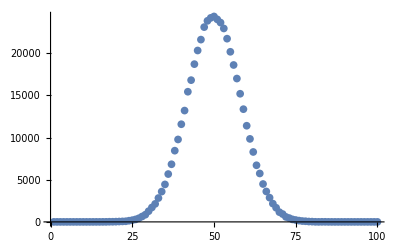

```mathematica
list1=Table[0,{100}];
i=0;
While[i<500000,
x=50;
j=0;
While[j<100,
x+=RandomInteger[{-1,1}];
j++];
list1[[x]]++
i++]
ListPlot[list1]
```

```mathematica
課題１
```

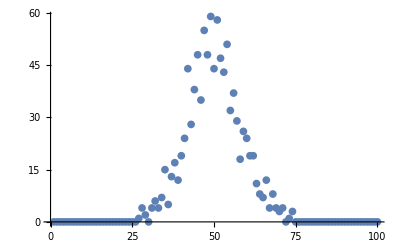

ReplaceAll::reps: は置換則リストあるいは有効なディスパッチテーブルではないため，置換に使用できません．

General::ivar: 55は有効な変数ではありません．

FindFit[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,4,2,0,4,6,4,7,15,5,13,17,12,19,24,44,28,38,48,35,55,48,59,44,58,47,43,51,32,37,29,18,26,24,19,19,11,8,7,12,4,8,4,3,4,0,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{a ⅇ^(-3025 b),a ⅇ^(-b (5+c)^2)/.-Graphics-},{a,b,c},55]

```mathematica
list1=Table[0,{100}];
i=0;
While[i<1000,
x=50;
j=0;
While[j<100,
x+=RandomInteger[{-1,1}];
j++];
list1[[x]]++
i++]
graph1=ListPlot[list1]
FindFit[list1,{a*Exp[-b*x^2],a*Exp[-b*(x-50+c)^2]/.%},{a,b,c},x]
```

```mathematica
i=0;
j=0;
While[i<100000,
x=RandomReal[{0,1}];
y=RandomReal[{0,1}];
If[x<y,j++];
If[x==y,j=j+1/2];
i++]
N[j/i]
```

0.50082

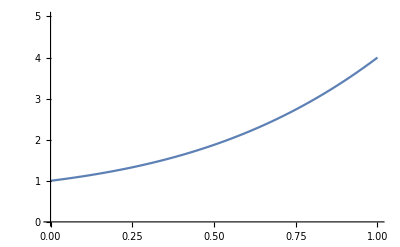

2.08333

```mathematica
func2[k_]:=k^3+k^2+k+1;
Plot[func2[x],{x,0,1},PlotRange->{0,5}]
NIntegrate[func2[x],{x,0,1}]
```

```mathematica
func2[k_]:=k^3+k^2+k+1;
i=0;
j=0;
While[i<1000000,
x=RandomReal[{0,1}];
y=RandomReal[{0,5}];
If[y<func2[x],j++];
If[y==func2[x],j=j+1/2];
i++]
N[5 j/i]
```

2.08594

```mathematica
課題２
```

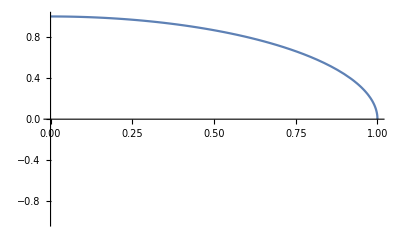

1.5708

```mathematica
func3[k_]:=√(1^2-k^2);
Plot[func3[x],{x,0,1},PlotRange->{-1,1}]
NIntegrate[func3[x],{x,-1,1}]
```

```mathematica
func3[k_]:=√(1^2-k^2);
i=0;
j=0;
While[i<1000000,
x=RandomReal[{0,1}];
y=RandomReal[{0,1}];
If[y<func3[x],j++];
If[y==func3[x],j=j+1/2];
i++]
N[4 j/i]
```

3.1427

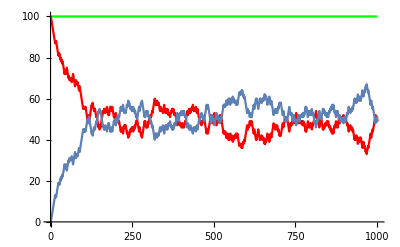

```mathematica
i=0;
hidari=100;migi=0;
list2={};list3={};list4={};
AppendTo[list2,hidari];
AppendTo[list3,migi];
While[i<1000,wariai=hidari/(hidari+migi);
If[wariai>RandomReal[{0,1}],
{hidari--;migi++},
{hidari++;migi--}];
AppendTo[list2,hidari];
AppendTo[list3,migi];
AppendTo[list4,hidari+migi];i++]
graph1=ListPlot[list2,Joined->True,PlotRange->{0,100},PlotStyle->RGBColor[{1,0,0}]];
graph2=ListPlot[list3,Joined->True,PlotRange->{0,100}];
graph3=ListPlot[list4,Joined->True,PlotRange->{0,100},PlotStyle->RGBColor[{0,1,0}]];
Show[graph1,graph2,graph3]
```

{}

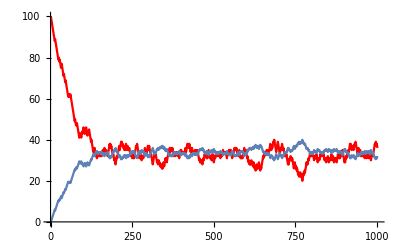

```mathematica
i=0;
hidari=100;migi=0;
list2={};list3={}
AppendTo[list2,hidari];
AppendTo[list3,migi/2];
While[i<1000,wariai=hidari/(hidari+migi/2);
If[wariai>RandomReal[{0,1}],
{hidari--;migi++},
{hidari++;migi--}];
AppendTo[list2,hidari];
AppendTo[list3,migi/2];i++];
graph1=ListPlot[list2,Joined->True,PlotRange->{0,100},PlotStyle->RGBColor[{1,0,0}]];
graph2=ListPlot[list3,Joined->True,PlotRange->{0,100}];
Show[graph1,graph2]
```

```mathematica
課題３
```

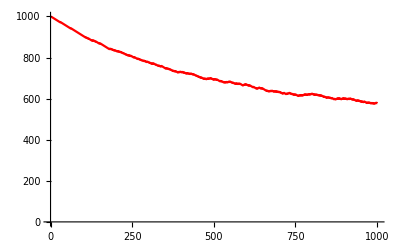

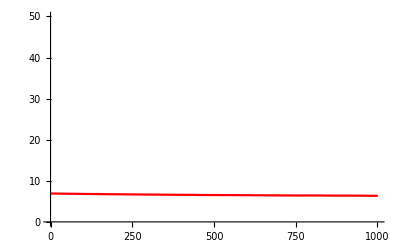

```mathematica
i=0;
hidari=1000;migi=0;
list5={};list6={};list7={};
AppendTo[list5,hidari];
AppendTo[list6,migi];
While[i<1000,wariai=hidari/1000;
If[wariai>RandomReal[{0,1}],
{hidari--;migi++},
{hidari++;migi--}];
AppendTo[list5,hidari];
AppendTo[list6,migi];
AppendTo[list7,hidari+migi];i++]
graph4=ListPlot[list5,Joined->True,PlotRange->{0,1000},PlotStyle->RGBColor[{1,0,0}]];
graph5=ListPlot[list6,Joined->True,PlotRange->{0,1000}];
graph6=ListPlot[list7,Joined->True,PlotRange->{0,1000},PlotStyle->RGBColor[{0,1,0}]];
Show[graph4]
graph7=ListPlot[Log[list5],Joined->True,PlotRange->{{0,1000},{0,50}},PlotStyle->RGBColor[{1,0,0}]];
Show[graph7]
```